```mathematica
steps[nsteps_]:=Module[{path,randsteps},
path={{0,0}};
Do[randstep=RandomChoice[{{0,1},{0,-1},{1,0},{-1,0}}];
AppendTo[path,Last[path]+randstep],{i,1,nsteps}];
Print["The number of steps is ",nsteps];
finalpoint=Last[path];
path]
```

The number of steps is 100

{{0,0},{-1,0},{-2,0},{-2,1},{-2,0},{-2,1},{-2,0},{-3,0},{-3,1},{-4,1},{-4,0},{-4,-1},{-4,0},{-4,-1},{-4,0},{-5,0},{-6,0},{-7,0},{-6,0},{-6,1},{-7,1},{-7,0},{-8,0},{-7,0},{-7,1},{-6,1},{-6,0},{-6,-1},{-7,-1},{-7,0},{-8,0},{-9,0},{-9,-1},{-9,0},{-10,0},{-11,0},{-11,-1},{-10,-1},{-10,0},{-10,1},{-9,1},{-9,2},{-8,2},{-8,1},{-8,2},{-8,3},{-7,3},{-8,3},{-9,3},{-10,3},{-9,3},{-8,3},{-8,4},{-8,5},{-9,5},{-8,5},{-8,6},{-8,7},{-8,6},{-9,6},{-9,5},{-10,5},{-10,4},{-10,3},{-10,2},{-9,2},{-8,2},{-8,3},{-7,3},{-7,2},{-7,3},{-7,2},{-8,2},{-7,2},{-8,2},{-8,3},{-8,2},{-8,3},{-8,4},{-7,4},{-6,4},{-7,4},{-6,4},{-6,3},{-6,4},{-6,3},{-5,3},{-5,2},{-4,2},{-4,3},{-5,3},{-5,2},{-4,2},{-3,2},{-3,3},{-3,4},{-2,4},{-2,3},{-2,4},{-3,4},{-3,3}}

The number of steps is 1000

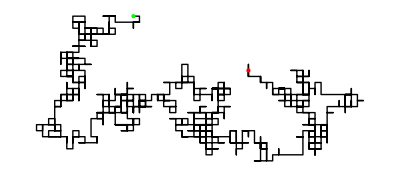

```mathematica
Graphics[{Line[steps[10000]],{Red,Point[{0,0}]},{Green,Point[finalpoint]}}]
```

```mathematica
steps3D[nsteps_]:=Module[{path,randsteps},
path={{0,0,0}};
Do[randstep=RandomChoice[{{0,1,0},{0,-1,0},{1,0,0},{-1,0,0},{0,0,1},{0,0,-1}}];
AppendTo[path,Last[path]+randstep],{i,1,nsteps}];
Print["The number of steps is ",nsteps];
finalpoint3D=Last[path];
path]
```

```mathematica
steps3D[100]
```

The number of steps is 100

{{0,0,0},{0,0,-1},{0,0,-2},{0,0,-3},{-1,0,-3},{-1,0,-4},{-1,0,-5},{-1,0,-4},{-1,1,-4},{-1,1,-5},{-1,1,-4},{0,1,-4},{0,1,-5},{0,1,-6},{1,1,-6},{2,1,-6},{3,1,-6},{4,1,-6},{3,1,-6},{3,2,-6},{2,2,-6},{2,2,-5},{3,2,-5},{3,2,-4},{3,1,-4},{2,1,-4},{2,1,-3},{2,2,-3},{2,1,-3},{2,1,-2},{2,1,-3},{2,1,-2},{2,1,-1},{2,0,-1},{2,-1,-1},{2,-2,-1},{2,-1,-1},{2,-1,-2},{1,-1,-2},{1,-1,-3},{1,0,-3},{2,0,-3},{2,1,-3},{2,1,-4},{2,0,-4},{1,0,-4},{1,1,-4},{1,1,-3},{1,1,-4},{0,1,-4},{1,1,-4},{1,1,-5},{1,2,-5},{2,2,-5},{3,2,-5},{3,2,-4},{3,3,-4},{3,2,-4},{2,2,-4},{1,2,-4},{0,2,-4},{-1,2,-4},{-1,3,-4},{-2,3,-4},{-2,3,-3},{-2,3,-2},{-2,3,-1},{-2,3,0},{-2,2,0},{-2,2,1},{-2,1,1},{-2,0,1},{-2,0,2},{-3,0,2},{-3,0,3},{-3,1,3},{-4,1,3},{-4,1,4},{-4,2,4},{-3,2,4},{-3,2,3},{-3,3,3},{-3,4,3},{-2,4,3},{-3,4,3},{-3,4,4},{-2,4,4},{-3,4,4},{-3,5,4},{-3,5,3},{-2,5,3},{-2,4,3},{-3,4,3},{-3,3,3},{-2,3,3},{-1,3,3},{-1,4,3},{-1,5,3},{0,5,3},{0,6,3},{0,6,2}}

```mathematica
Graphics3D[{Line[steps3D[5000]],{Red,Point[{0,0,0}]},{Green,Point[finalpoint3D]}}]
```

The number of steps is 5000

-Graphics3D-